```mathematica
LogisticSigmoid[x]//FunctionExpand
```

1/(1+ⅇ^-x)

```mathematica
h[x_]:= 1/(1+ⅇ^-x)
```

```mathematica
?h
```

```mathematica
h[1]//N
```

0.731059

```mathematica
N[1/(1+1/ⅇ)]
```

0.731059

0.731059

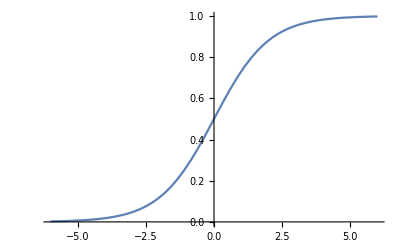

```mathematica
h[x_]:=1/(1+E^(-x))
h[1]//N
Plot[h[x],{x,-6,6}]
```